```mathematica
(*ЗАДАНИЕ 1*)
```

```mathematica
∫_0^π x √(cos^2 3x+4)ⅆx
```

(2 (64+(4+3 cos^2 π)^(3/2) (-8+9 cos^2 π)))/(135 cos^4)

```mathematica
∫_0^1 ∫_(-x^2)^x (12xy+27 x^2 y^2)ⅆxⅆy
```

3 x (x^2+x^5+4 xy+4 x xy)

```mathematica
Integrate[x*Sqrt[Cos[3x]^2+4],x] (*Вычисление интеграла аналитически*)
```

∫x √(4+Cos[3 x]^2)ⅆx

```mathematica
N[%]
```

∫x √(4+Cos[3 x]^2)ⅆx

```mathematica
Integrate[(12xy+27 x^2 y^2),{y,0,1},{x,-x^2,x} ](*Вычисление интеграла аналитически*)
```

3 x (x^2+x^5+4 xy+4 x xy)

```mathematica
Clear[x,y]
```

```mathematica
NIntegrate[(12x y+27x^2y^2),{y,0,1},{x,-x^2,x}]
```

NIntegrate::nlim: x = -x^2 is not a valid limit of integration.

NIntegrate[12 x y+27 x^2 y^2,{y,0,1},{x,-x^2,x}]

```mathematica
NIntegrate[12 x y+27 x^2 y^2,{y,-5^2,1},{x,0,1}]
```

45006.

```mathematica
NIntegrate[12 x y+27 x^2 y^2,{y,-x^2,x},{x,0,1}]
```

NIntegrate::nlim: y = -x^2 is not a valid limit of integration.

NIntegrate[12 x y+27 x^2 y^2,{y,-x^2,x},{x,0,1}]

```mathematica
NIntegrate[x*Sqrt[Cos[3x]^2+4],{x,0,π}] (*Вычисление интеграла численно*)
```

10.4602

```mathematica
Clear[x,y]
```

Set::write: Tag Times in f\ x is Protected.

Sin^2 x

Set::write: Tag Times in g\ x is Protected.

1-3 x+x^3

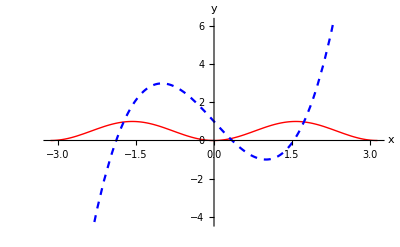

```mathematica
(*ЗАДАНИЕ 2*)
f(x)=Sin^2 x
g(x)=x^3-3x+1
Plot[{Sin[x]^2,x^3-3x+1},{x,-π,π},
PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed]},
AxesLabel->{Style["x",FontFamily->"Arial",FontSize->14],
Style["y",FontFamily->"Arial",FontSize->14]}]
```

```mathematica
Clear[x,y,f,g]
```

```mathematica
(*ЗАДАНИЕ 3*)
```

```mathematica
DD=Import["C:\\Users\\Home\\Documents\\Old.xlsx"]
```

{{{имя,столбец 1,столбец 2,столбец 3,столбец 4,столбец 5},{строка 1,12.,13.,14.,15.,16.},{строка 2,17.,18.,19.,20.,21.},{строка 3,22.,23.,24.,25.,26.},{строка 4,27.,28.,29.,30.,31.},{строка 5,32.,33.,34.,35.,36.},{строка 6,37.,38.,39.,40.,41.},{строка 7,42.,43.,44.,45.,46.},{строка 8,47.,48.,49.,50.,51.},{строка 9,52.,53.,54.,55.,56.},{строка 10,57.,58.,59.,60.,61.}}}

```mathematica
NDD=DD[[1]]
```

{{имя,столбец 1,столбец 2,столбец 3,столбец 4,столбец 5},{строка 1,12.,13.,14.,15.,16.},{строка 2,17.,18.,19.,20.,21.},{строка 3,22.,23.,24.,25.,26.},{строка 4,27.,28.,29.,30.,31.},{строка 5,32.,33.,34.,35.,36.},{строка 6,37.,38.,39.,40.,41.},{строка 7,42.,43.,44.,45.,46.},{строка 8,47.,48.,49.,50.,51.},{строка 9,52.,53.,54.,55.,56.},{строка 10,57.,58.,59.,60.,61.}}

```mathematica
NDD//MatrixForm
```

(имя | столбец 1 | столбец 2 | столбец 3 | столбец 4 | столбец 5
строка 1 | 12. | 13. | 14. | 15. | 16.
строка 2 | 17. | 18. | 19. | 20. | 21.
строка 3 | 22. | 23. | 24. | 25. | 26.
строка 4 | 27. | 28. | 29. | 30. | 31.
строка 5 | 32. | 33. | 34. | 35. | 36.
строка 6 | 37. | 38. | 39. | 40. | 41.
строка 7 | 42. | 43. | 44. | 45. | 46.
строка 8 | 47. | 48. | 49. | 50. | 51.
строка 9 | 52. | 53. | 54. | 55. | 56.
строка 10 | 57. | 58. | 59. | 60. | 61.)

```mathematica
NDD=Drop[NDD,{1},{1}] //MatrixForm
```

(12. | 13. | 14. | 15. | 16.
17. | 18. | 19. | 20. | 21.
22. | 23. | 24. | 25. | 26.
27. | 28. | 29. | 30. | 31.
32. | 33. | 34. | 35. | 36.
37. | 38. | 39. | 40. | 41.
42. | 43. | 44. | 45. | 46.
47. | 48. | 49. | 50. | 51.
52. | 53. | 54. | 55. | 56.
57. | 58. | 59. | 60. | 61.)

```mathematica
Transpose[NDD[[1]]]//MatrixForm
```

(12. | 17. | 22. | 27. | 32. | 37. | 42. | 47. | 52. | 57.
13. | 18. | 23. | 28. | 33. | 38. | 43. | 48. | 53. | 58.
14. | 19. | 24. | 29. | 34. | 39. | 44. | 49. | 54. | 59.
15. | 20. | 25. | 30. | 35. | 40. | 45. | 50. | 55. | 60.
16. | 21. | 26. | 31. | 36. | 41. | 46. | 51. | 56. | 61.)

```mathematica
NewList=NDD[[{1,1},{1,2}]]//MatrixForm
```

(12. | 13. | 14. | 15. | 16.
17. | 18. | 19. | 20. | 21.)

```mathematica
Dimensions[NewList]
```

{1,2}

```mathematica
NO=NewList[[1,2]]
```

{{12.,13.,14.,15.,16.},{17.,18.,19.,20.,21.}}

```mathematica
Dim=Dimensions[NO]
```

{2,5}

```mathematica
Dim[[2]]
```

5

```mathematica
AddN=Table[i^2, {i, Dim[[2]]}]
```

{1,4,9,16,25}

```mathematica
T=Join[NO,{AddN}]
```

{{12.,13.,14.,15.,16.},{17.,18.,19.,20.,21.},{1,4,9,16,25}}

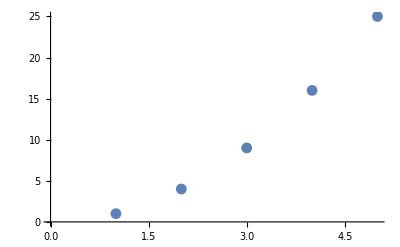

```mathematica
ListPlot[AddN]
```

```mathematica
Dimensions[AddList[[1,1]]]
```

{5}

```mathematica
New=Join[NewList,AddList,3]//MatrixForm
```

Join::headsd: Expression 144. | 169. | 196. | 225. | 256.
289. | 324. | 361. | 400. | 441.
484. | 529. | 576. | 625. | 676.
729. | 784. | 841. | 900. | 961.
1024. | 1089. | 1156. | 1225. | 1296.
1369. | 1444. | 1521. | 1600. | 1681.
1764. | 1849. | 1936. | 2025. | 2116.
2209. | 2304. | 2401. | 2500. | 2601.
2704. | 2809. | 2916. | 3025. | 3136.
3249. | 3364. | 3481. | 3600. | 3721. at position 2 is expected to have head MatrixForm for all expressions at level 3.

Join[(12. | 13. | 14. | 15. | 16.
17. | 18. | 19. | 20. | 21.),(144. | 169. | 196. | 225. | 256.
289. | 324. | 361. | 400. | 441.
484. | 529. | 576. | 625. | 676.
729. | 784. | 841. | 900. | 961.
1024. | 1089. | 1156. | 1225. | 1296.
1369. | 1444. | 1521. | 1600. | 1681.
1764. | 1849. | 1936. | 2025. | 2116.
2209. | 2304. | 2401. | 2500. | 2601.
2704. | 2809. | 2916. | 3025. | 3136.
3249. | 3364. | 3481. | 3600. | 3721.),3]

```mathematica
Dimensions[NDD[[1]]]
```

{10,5}

```mathematica
`
```

Set::write: Tag Times in g\ x is Protected.

Set::write: Tag Times in f\ x is Protected.

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Set::write: Tag Times in f\ x is Protected.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.08099×10^-16 and 1.13268×10^-17 for the integral and error estimates.

6.